# HW 1_1

3.1

SparseArray[…]

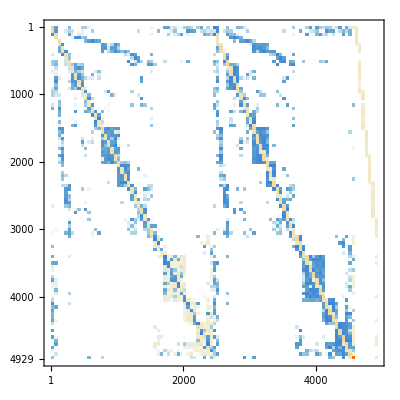

0.00136011

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/gemat/gemat12.mtx.gz"]
MatrixPlot[A]
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\Numerical-Linear-Algebra\\MA5627_4610\\SolutionsAndExamples\\Week 1"];
Export["gemat12.mtx",A];
A["Density"]
```

3.2

```mathematica
{m,n}=Dimensions[A];
b=SparseArray[1->1.0,n];
```

3.3

```mathematica
{Eigenvalues[A,{3}],Eigenvalues[A,3]⟦3⟧}
```

{{5.2894-1.20544 ⅈ},5.2894-1.20544 ⅈ}

3.4

```mathematica
x=LinearSolve[A,b];x⟦3⟧
```

1.11486

3.5

{0.78125,Null}

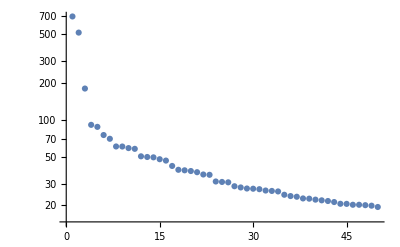

```mathematica
Timing[σs= SingularValueList[A,50];]
ListLogPlot[ σs]
```

3.6

```mathematica
Timing[σs= SingularValueList[A];]
```

SingularValueList::arh: Because finding 4929 out of the 4929 singular values and/or singular vectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer singular values and/or singular vectors would be sufficient, consider restricting this number using the second argument to SingularValueList.

{50.0469,Null}